```mathematica
optsLabel1=Sequence[FontFamily->"Helvetica",FontSize->22];
optsLabel2=Sequence[FontFamily->"Helvetica",FontSize->22,Transparent];
optsCentrality=Sequence[FontFamily->"Helvetica",FontSize->18];
optsCentrality2=Sequence[FontFamily->"Helvetica",FontSize->18,Transparent];
optsScale1=Sequence[FontFamily->"Helvetica",FontSize->16];
optsScale2=Sequence[FontFamily->"Helvetica",FontSize->16,Transparent];
```

```mathematica
Clear[c,ct,α,ω,p,s,ϕMC,KRC,γ]
```

```mathematica
c=α/4(√(1+(8ct)/α)-1)
```

1/4 (-1+√(1+(8 ct)/α)) α

```mathematica
M=ϕMC r1(1+c^2 1/p+ω/p c^4)/(1+c^2(1+1/p)+ω/p c^4)
R=KRC ct
```

(r1 ϕMC (1+((-1+√(1+(8 ct)/α))^2 α^2)/(16 p)+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))/(1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p))

ct KRC

```mathematica
M/R
```

(r1 ϕMC (1+((-1+√(1+(8 ct)/α))^2 α^2)/(16 p)+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))/(ct KRC (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))

```mathematica
α=4.2
ω=1.
p=5.
```

4.2

1.

5.

We selected KRC such that the M/R ratio starts at 1; however, this is an overall multiplicative constant which does not affect the dynamics.

```mathematica
ϕMC=1.
KRC=0.049994995642660474/0.010004957239254023
```

1.

4.99702

```mathematica
s=0.2
```

0.2

```mathematica
Clear[r1]
```

```mathematica
ee=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/α))^2 α^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))==0,ct,Reals]},{r1,0.05,5.1,0.05}]
```

{{0.05,{{ct→0.010005}}},{0.1,{{ct→0.0200394}}},{0.15,{{ct→0.0301323}}},{0.2,{{ct→0.0403125}}},{0.25,{{ct→0.0506094}}},{0.3,{{ct→0.0610531}}},{0.35,{{ct→0.0716752}}},{0.4,{{ct→0.082509}}},{0.45,{{ct→0.0935904}}},{0.5,{{ct→0.104958}}},{0.55,{{ct→0.116655}}},{0.6,{{ct→0.128728}}},{0.65,{{ct→0.14123}}},{0.7,{{ct→0.15422}}},{0.75,{{ct→0.167766}}},{0.8,{{ct→0.181946}}},{0.85,{{ct→0.196848}}},{0.9,{{ct→0.212577}}},{0.95,{{ct→0.229252}}},{1.,{{ct→0.247017}}},{1.05,{{ct→0.266037}}},{1.1,{{ct→0.28651}}},{1.15,{{ct→0.308666}}},{1.2,{{ct→0.332776}}},{1.25,{{ct→0.35915}}},{1.3,{{ct→0.388138}}},{1.35,{{ct→0.420114}}},{1.4,{{ct→0.455447}}},{1.45,{{ct→0.494446}}},{1.5,{{ct→0.537289}}},{1.55,{{ct→0.58393}}},{1.6,{{ct→0.634044}}},{1.65,{{ct→0.687038}}},{1.7,{{ct→0.742137}}},{1.75,{{ct→0.798524}}},{1.8,{{ct→0.855464}}},{1.85,{{ct→0.912368}}},{1.9,{{ct→0.968815}}},{1.95,{{ct→1.02452}}},{2.,{{ct→1.07933}}},{2.05,{{ct→1.13313}}},{2.1,{{ct→1.18591}}},{2.15,{{ct→1.23766}}},{2.2,{{ct→1.28839}}},{2.25,{{ct→1.33815}}},{2.3,{{ct→1.38697}}},{2.35,{{ct→1.43489}}},{2.4,{{ct→1.48196}}},{2.45,{{ct→1.52822}}},{2.5,{{ct→1.57371}}},{2.55,{{ct→1.61847}}},{2.6,{{ct→1.66253}}},{2.65,{{ct→1.70594}}},{2.7,{{ct→1.74871}}},{2.75,{{ct→1.79088}}},{2.8,{{ct→1.83249}}},{2.85,{{ct→1.87354}}},{2.9,{{ct→1.91408}}},{2.95,{{ct→1.95411}}},{3.,{{ct→1.99367}}},{3.05,{{ct→2.03277}}},{3.1,{{ct→2.07143}}},{3.15,{{ct→2.10966}}},{3.2,{{ct→2.14749}}},{3.25,{{ct→2.18492}}},{3.3,{{ct→2.22198}}},{3.35,{{ct→2.25867}}},{3.4,{{ct→2.295}}},{3.45,{{ct→2.331}}},{3.5,{{ct→2.36667}}},{3.55,{{ct→2.40202}}},{3.6,{{ct→2.43706}}},{3.65,{{ct→2.4718}}},{3.7,{{ct→2.50625}}},{3.75,{{ct→2.54042}}},{3.8,{{ct→2.57432}}},{3.85,{{ct→2.60794}}},{3.9,{{ct→2.64131}}},{3.95,{{ct→2.67443}}},{4.,{{ct→2.70731}}},{4.05,{{ct→2.73994}}},{4.1,{{ct→2.77235}}},{4.15,{{ct→2.80452}}},{4.2,{{ct→2.83648}}},{4.25,{{ct→2.86822}}},{4.3,{{ct→2.89975}}},{4.35,{{ct→2.93108}}},{4.4,{{ct→2.9622}}},{4.45,{{ct→2.99313}}},{4.5,{{ct→3.02387}}},{4.55,{{ct→3.05442}}},{4.6,{{ct→3.08479}}},{4.65,{{ct→3.11497}}},{4.7,{{ct→3.14499}}},{4.75,{{ct→3.17483}}},{4.8,{{ct→3.2045}}},{4.85,{{ct→3.23401}}},{4.9,{{ct→3.26335}}},{4.95,{{ct→3.29254}}},{5.,{{ct→3.32157}}},{5.05,{{ct→3.35045}}},{5.1,{{ct→3.37919}}}}

```mathematica
ee1Down={{0.05,0.010004957239254023},{0.1,0.02003939048130601},{0.15000000000000002,0.030132279397496648},{0.2,0.040312522583876895},{0.25,0.050609418665749174},{0.3,0.06105313851927915},{0.35000000000000003,0.07167520725547974},{0.4,0.08250901393746521},{0.45,0.09359036752958982},{0.5,0.1049581192213937},{0.55,0.1166548740391789},{0.6000000000000001,0.12872781863133295},{0.6500000000000001,0.14122969740997054},{0.7000000000000001,0.15421997597063},{0.7500000000000001,0.16776623893223194},{0.8,0.18194587883758367},{0.8500000000000001,0.19684814276442003},{0.9000000000000001,0.21257661186678214},{0.9500000000000001,0.22925219186960158},{1.,0.2470166806551421},{1.05,0.2660369349890789},{1.1,0.28650954914801946},{1.1500000000000001,0.30866572454118296},{1.2000000000000002,0.33277555239743484},{1.2500000000000002,0.3591501052890206},{1.3,0.3881383775551055},{1.35,0.42011421541333777},{1.4000000000000001,0.45544651205705017},{1.4500000000000002,0.49444609239302567},{1.5000000000000002,0.5372887804007821}};
ee1Middle={{1.5000000000000002,0.5372887804007821},{1.55,0.5839296979606325},{1.6,0.6340443467854638},{1.6500000000000001,0.6870380196575905},{1.7000000000000002,0.7421367422748754},{1.7500000000000002,0.7985240510746148},{1.8,0.8554635960272444},{1.85,0.9123683017054248},{1.9000000000000001,0.9688147339453006},{1.9500000000000002,1.0245232733642642},{2.,1.0793256315870188},{2.05,1.1331329649213095},{2.1,1.1859099807554088},{2.15,1.237655882701093},{2.1999999999999997,1.2883911351295005},{2.25,1.3381486010623966},{2.3,1.3869677598073222},{2.35,1.4348910143884968}};
ee1Up={{2.35,1.4348910143884968},{2.4,1.4819613856636984},{2.45,1.5282211133225132},{2.5,1.5737108435994154},{2.55,1.618469192767502},{2.6,1.66253254847368},{2.65,1.7059350191394935},{2.7,1.7487084732260758},{2.75,1.7908826308002592},{2.8,1.8324851833146254},{2.85,1.873541926309522},{2.9,1.9140768954818907},{2.95,1.9541125003016},{3.,1.9936696517804628},{3.05,2.032767882562789},{3.1,2.0714254585043985},{3.15,2.1096594815334617},{3.2,2.1474859839692026},{3.25,2.1849200146978918},{3.3,2.221975717725576},{3.35,2.258666403680707},{3.4,2.295004614851788},{3.45,2.3310021843315263},{3.5,2.3666702898104806},{3.55,2.4020195025267204},{3.6,2.4370598318380865},{3.65,2.4718007658430654},{3.7,2.5062513084368176},{3.75,2.540420013151511},{3.8,2.5743150140953492},{3.85,2.6079440542727994},{3.9,2.6413145115394823},{3.95,2.6744334224189705},{4.,2.7073075039851484},{4.05,2.7399431739926294},{4.1,2.7723465694188243},{4.15,2.8045235635643477},{4.2,2.8364797818434035},{4.25,2.86822061638235},{4.3,2.8997512395326854},{4.35,2.9310766163940256},{4.4,2.962201516433136},{4.45,2.993130524276608},{4.5,3.023868049747189},{4.55,3.054418337207023},{4.6,3.0847854742650234},{4.65,3.1149733999001787},{4.7,3.1449859120477646},{4.75,3.1748266746910927},{4.8,3.2044992244975345},{4.8500000000000005,3.23400697703406},{4.9,3.2633532325943873},{4.95,3.2925411816670103},{5.,3.3215739100708146},{5.05,3.3504544037826998},{5.1000000000000005,3.3791855534795356}};
```

```mathematica
NMaxU=Length[ee1Up]
NMaxM=Length[ee1Middle]
NMaxD=Length[ee1Down]
```

56

18

30

```mathematica
RUp=Table[{ee1Up[[i,1]],KRC ee1Up[[i,2]]},{i,1,NMaxU}]
```

{{2.35,7.17018},{2.4,7.40539},{2.45,7.63656},{2.5,7.86387},{2.55,8.08753},{2.6,8.30771},{2.65,8.5246},{2.7,8.73834},{2.75,8.94908},{2.8,9.15697},{2.85,9.36213},{2.9,9.56469},{2.95,9.76474},{3.,9.96241},{3.05,10.1578},{3.1,10.351},{3.15,10.542},{3.2,10.731},{3.25,10.9181},{3.3,11.1033},{3.35,11.2866},{3.4,11.4682},{3.45,11.6481},{3.5,11.8263},{3.55,12.0029},{3.6,12.178},{3.65,12.3516},{3.7,12.5238},{3.75,12.6945},{3.8,12.8639},{3.85,13.032},{3.9,13.1987},{3.95,13.3642},{4.,13.5285},{4.05,13.6916},{4.1,13.8535},{4.15,14.0143},{4.2,14.174},{4.25,14.3326},{4.3,14.4901},{4.35,14.6467},{4.4,14.8022},{4.45,14.9567},{4.5,15.1103},{4.55,15.263},{4.6,15.4147},{4.65,15.5656},{4.7,15.7156},{4.75,15.8647},{4.8,16.013},{4.85,16.1604},{4.9,16.307},{4.95,16.4529},{5.,16.598},{5.05,16.7423},{5.1,16.8859}}

```mathematica
RMiddle=Table[{ee1Middle[[i,1]],KRC ee1Middle[[i,2]]},{i,1,NMaxM}]
```

{{1.5,2.68484},{1.55,2.91791},{1.6,3.16833},{1.65,3.43314},{1.7,3.70847},{1.75,3.99024},{1.8,4.27477},{1.85,4.55912},{1.9,4.84119},{1.95,5.11957},{2.,5.39341},{2.05,5.66229},{2.1,5.92602},{2.15,6.18459},{2.2,6.43812},{2.25,6.68676},{2.3,6.93071},{2.35,7.17018}}

```mathematica
RDown=Table[{ee1Down[[i,1]],KRC ee1Down[[i,2]]},{i,1,NMaxD}]
```

{{0.05,0.049995},{0.1,0.100137},{0.15,0.150572},{0.2,0.201443},{0.25,0.252896},{0.3,0.305084},{0.35,0.358163},{0.4,0.412299},{0.45,0.467673},{0.5,0.524478},{0.55,0.582927},{0.6,0.643256},{0.65,0.705728},{0.7,0.770641},{0.75,0.838332},{0.8,0.909188},{0.85,0.983655},{0.9,1.06225},{0.95,1.14558},{1.,1.23435},{1.05,1.32939},{1.1,1.43169},{1.15,1.54241},{1.2,1.66289},{1.25,1.79468},{1.3,1.93954},{1.35,2.09932},{1.4,2.27588},{1.45,2.47076},{1.5,2.68484}}

```mathematica
MUp=Table[{ee1Up[[i,1]],(ϕMC ee1Up[[i,1]](1+(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^2 1/p+ω/p(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^4))/(1+(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^2(1+1/p)+ω/p(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^4)},{i,1,NMaxU}]
```

{{2.35,1.38511},{2.4,1.39804},{2.45,1.41178},{2.5,1.42629},{2.55,1.44153},{2.6,1.45747},{2.65,1.47406},{2.7,1.49129},{2.75,1.50912},{2.8,1.52751},{2.85,1.54646},{2.9,1.56592},{2.95,1.58589},{3.,1.60633},{3.05,1.62723},{3.1,1.64857},{3.15,1.67034},{3.2,1.69251},{3.25,1.71508},{3.3,1.73802},{3.35,1.76133},{3.4,1.785},{3.45,1.809},{3.5,1.83333},{3.55,1.85798},{3.6,1.88294},{3.65,1.9082},{3.7,1.93375},{3.75,1.95958},{3.8,1.98568},{3.85,2.01206},{3.9,2.03869},{3.95,2.06557},{4.,2.09269},{4.05,2.12006},{4.1,2.14765},{4.15,2.17548},{4.2,2.20352},{4.25,2.23178},{4.3,2.26025},{4.35,2.28892},{4.4,2.3178},{4.45,2.34687},{4.5,2.37613},{4.55,2.40558},{4.6,2.43521},{4.65,2.46503},{4.7,2.49501},{4.75,2.52517},{4.8,2.5555},{4.85,2.58599},{4.9,2.61665},{4.95,2.64746},{5.,2.67843},{5.05,2.70955},{5.1,2.74081}}

```mathematica
MMiddle=Table[{ee1Middle[[i,1]],(ϕMC ee1Middle[[i,1]](1+(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^2 1/p+ω/p(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^4))/(1+(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^2(1+1/p)+ω/p(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^4)},{i,1,NMaxM}]
```

{{1.5,1.26271},{1.55,1.27607},{1.6,1.28596},{1.65,1.29296},{1.7,1.29786},{1.75,1.30148},{1.8,1.30454},{1.85,1.30763},{1.9,1.31119},{1.95,1.31548},{2.,1.32067},{2.05,1.32687},{2.1,1.33409},{2.15,1.34234},{2.2,1.35161},{2.25,1.36185},{2.3,1.37303},{2.35,1.38511}}

```mathematica
MDown=Table[{ee1Down[[i,1]],(ϕMC ee1Down[[i,1]](1+(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^2 1/p+ω/p(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^4))/(1+(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^2(1+1/p)+ω/p(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^4)},{i,1,NMaxD}]
```

{{0.05,0.049995},{0.1,0.0999606},{0.15,0.149868},{0.2,0.199687},{0.25,0.249391},{0.3,0.298947},{0.35,0.348325},{0.4,0.397491},{0.45,0.44641},{0.5,0.495042},{0.55,0.543345},{0.6,0.591272},{0.65,0.63877},{0.7,0.68578},{0.75,0.732234},{0.8,0.778054},{0.85,0.823152},{0.9,0.867423},{0.95,0.910748},{1.,0.952983},{1.05,0.993963},{1.1,1.03349},{1.15,1.07133},{1.2,1.10722},{1.25,1.14085},{1.3,1.17186},{1.35,1.19989},{1.4,1.22455},{1.45,1.24555},{1.5,1.26271}}

```mathematica
MRRatioUp=Table[{ee1Up[[i,1]],MUp[[i,2]]/RUp[[i,2]]},{i,1,NMaxU}]
```

{{2.35,0.193176},{2.4,0.188787},{2.45,0.184871},{2.5,0.181372},{2.55,0.178241},{2.6,0.175435},{2.65,0.172919},{2.7,0.170661},{2.75,0.168634},{2.8,0.166814},{2.85,0.165182},{2.9,0.163719},{2.95,0.16241},{3.,0.161239},{3.05,0.160196},{3.1,0.159268},{3.15,0.158446},{3.2,0.157721},{3.25,0.157086},{3.3,0.156533},{3.35,0.156055},{3.4,0.155648},{3.45,0.155305},{3.5,0.155021},{3.55,0.154794},{3.6,0.154618},{3.65,0.154489},{3.7,0.154406},{3.75,0.154364},{3.8,0.154361},{3.85,0.154394},{3.9,0.154461},{3.95,0.15456},{4.,0.154688},{4.05,0.154844},{4.1,0.155026},{4.15,0.155233},{4.2,0.155463},{4.25,0.155714},{4.3,0.155985},{4.35,0.156276},{4.4,0.156585},{4.45,0.15691},{4.5,0.157252},{4.55,0.157609},{4.6,0.15798},{4.65,0.158364},{4.7,0.158761},{4.75,0.15917},{4.8,0.15959},{4.85,0.16002},{4.9,0.160461},{4.95,0.160911},{5.,0.161371},{5.05,0.161838},{5.1,0.162314}}

```mathematica
MRRatioMiddle=Table[{ee1Middle[[i,1]],MMiddle[[i,2]]/RMiddle[[i,2]]},{i,1,NMaxM}]
```

{{1.5,0.470311},{1.55,0.437323},{1.6,0.405878},{1.65,0.376612},{1.7,0.349972},{1.75,0.326165},{1.8,0.305171},{1.85,0.286816},{1.9,0.27084},{1.95,0.256951},{2.,0.244868},{2.05,0.234334},{2.1,0.225124},{2.15,0.217046},{2.2,0.209938},{2.25,0.203664},{2.3,0.198108},{2.35,0.193176}}

```mathematica
MRRatioDown=Table[{ee1Down[[i,1]],MDown[[i,2]]/RDown[[i,2]]},{i,1,NMaxD}]
```

{{0.05,1.},{0.1,0.998236},{0.15,0.995325},{0.2,0.991287},{0.25,0.986137},{0.3,0.979884},{0.35,0.972533},{0.4,0.964083},{0.45,0.954533},{0.5,0.943875},{0.55,0.932098},{0.6,0.919187},{0.65,0.905123},{0.7,0.889883},{0.75,0.873442},{0.8,0.855768},{0.85,0.83683},{0.9,0.816591},{0.95,0.795011},{1.,0.772054},{1.05,0.747682},{1.1,0.721865},{1.15,0.694585},{1.2,0.665845},{1.25,0.635684},{1.3,0.604197},{1.35,0.571559},{1.4,0.538058},{1.45,0.504118},{1.5,0.470311}}

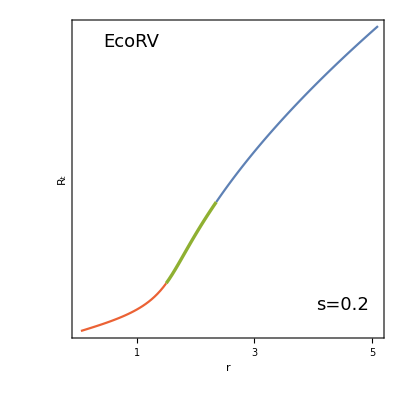

```mathematica
PlotREcoRV=Show[ListLinePlot[{RDown,RUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[RMiddle, PlotStyle->{ColorData[97,3],Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["R_t",optsLabel1]},FrameTicks->{
{None,None},

{{{5,StyleForm["5",optsScale1],{0.03,0}},{4,StyleForm["4",optsScale1],{0.03,0}},{3,StyleForm["3",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}},{1,StyleForm["1",optsScale1],{0.03,0}},{0,StyleForm["0",optsScale1],{0.03,0}}},None}},Epilog->{Text[StyleForm["EcoRV",optsCentrality],{0.9,16},{0,0}],Text[StyleForm["s=0.2",optsCentrality],{4.5,1.5},{0,0}]},AspectRatio->1]
```

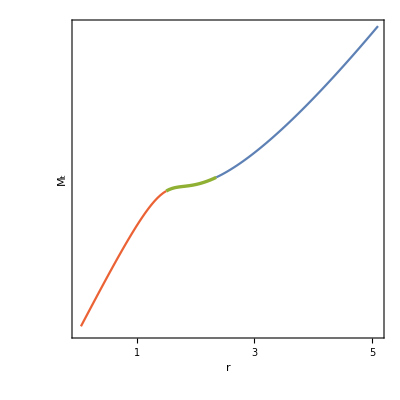

```mathematica
PlotMEcoRV=Show[ListLinePlot[{MDown,MUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MMiddle, PlotStyle->{ColorData[97,3],Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["M_t",optsLabel1]},FrameTicks->{
{None,None},
{{{5,StyleForm["5",optsScale1],{0.03,0}},{4,StyleForm["4",optsScale1],{0.03,0}},{3,StyleForm["3",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}},{1,StyleForm["1",optsScale1],{0.03,0}},{0,StyleForm["0",optsScale1],{0.03,0}}},None}},AspectRatio->1]
```

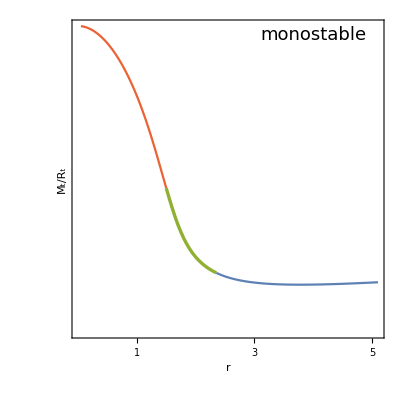

```mathematica
PlotMREcoRV=Show[ListLinePlot[{MRRatioDown,MRRatioUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MRRatioMiddle, PlotStyle->{ColorData[97,3],Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["M_t/R_t",optsLabel1]},FrameTicks->{
{None,None},

{{{5,StyleForm["5",optsScale1],{0.03,0}},{4,StyleForm["4",optsScale1],{0.03,0}},{3,StyleForm["3",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}},{1,StyleForm["1",optsScale1],{0.03,0}},{0,StyleForm["0",optsScale1],{0.03,0}}},None}},Epilog->{Text[StyleForm["monostable",optsCentrality],{4.,0.972},{0,0}]},AspectRatio->1]
```

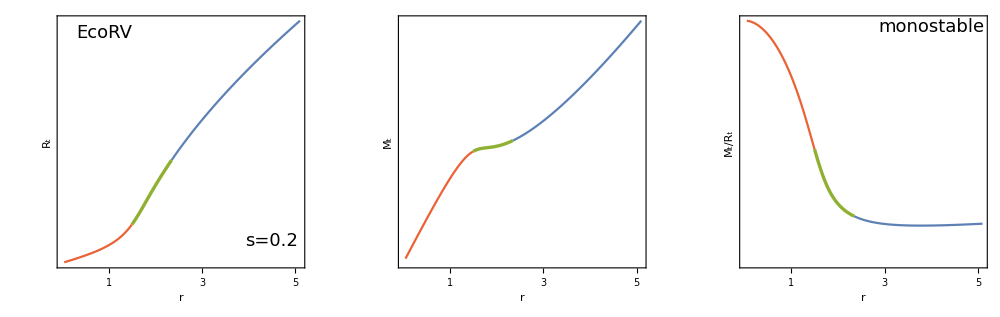

```mathematica
GraphicsRow[{PlotREcoRV,PlotMEcoRV,PlotMREcoRV},ImageSize->1000]
```

```mathematica
KRC=33.33076171298755
```

33.3308

```mathematica
s=0.03
```

0.03

```mathematica
Clear[r1]
```

```mathematica
ee=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/α))^2 α^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))==0,ct,Reals]},{r1,0.05,5.1,0.05}]
```

{{0.05,{{ct→0.00150011}}},{0.1,{{ct→0.0030009}}},{0.15,{{ct→0.00450303}}},{0.2,{{ct→0.00600718}}},{0.25,{{ct→0.00751401}}},{0.3,{{ct→0.00902422}}},{0.35,{{ct→0.0105385}}},{0.4,{{ct→0.0120575}}},{0.45,{{ct→0.0135819}}},{0.5,{{ct→0.0151125}}},{0.55,{{ct→0.0166501}}},{0.6,{{ct→0.0181952}}},{0.65,{{ct→0.0197487}}},{0.7,{{ct→0.0213115}}},{0.75,{{ct→0.0228842}}},{0.8,{{ct→0.0244678}}},{0.85,{{ct→0.026063}}},{0.9,{{ct→0.0276709}}},{0.95,{{ct→0.0292924}}},{1.,{{ct→0.0309283}}},{1.05,{{ct→0.0325799}}},{1.1,{{ct→0.0342481}}},{1.15,{{ct→0.0359341}}},{1.2,{{ct→0.037639}}},{1.25,{{ct→0.0393642}}},{1.3,{{ct→0.041111}}},{1.35,{{ct→0.0428808}}},{1.4,{{ct→0.0446751}}},{1.45,{{ct→0.0464957}}},{1.5,{{ct→0.0483441}}},{1.55,{{ct→0.0502222}}},{1.6,{{ct→0.0521322}}},{1.65,{{ct→0.0540761}}},{1.7,{{ct→0.0560563}}},{1.75,{{ct→0.0580754}}},{1.8,{{ct→0.0601361}}},{1.85,{{ct→0.0622415}}},{1.9,{{ct→0.064395}}},{1.95,{{ct→0.0666001}}},{2.,{{ct→0.0688611}}},{2.05,{{ct→0.0711823}}},{2.1,{{ct→0.0735689}}},{2.15,{{ct→0.0760266}}},{2.2,{{ct→0.0785616}}},{2.25,{{ct→0.0811813}}},{2.3,{{ct→0.0838939}}},{2.35,{{ct→0.086709}}},{2.4,{{ct→0.0896374}}},{2.45,{{ct→0.092692}}},{2.5,{{ct→0.0958879}}},{2.55,{{ct→0.0992431}}},{2.6,{{ct→0.102779}}},{2.65,{{ct→0.106523}}},{2.7,{{ct→0.110508}}},{2.75,{{ct→0.114774}}},{2.8,{{ct→0.119377},{ct→0.64009},{ct→0.847136}}},{2.85,{{ct→0.124388},{ct→0.544048},{ct→0.968304}}},{2.9,{{ct→0.129907},{ct→0.485763},{ct→1.05094}}},{2.95,{{ct→0.136076},{ct→0.440385},{ct→1.11976}}},{3.,{{ct→0.143114},{ct→0.401696},{ct→1.18077}}},{3.05,{{ct→0.151384},{ct→0.36674},{ct→1.23657}}},{3.1,{{ct→0.161574},{ct→0.333428},{ct→1.28856}}},{3.15,{{ct→0.175311},{ct→0.299275},{ct→1.33761}}},{3.2,{{ct→0.199657},{ct→0.256652},{ct→1.38429}}},{3.25,{{ct→1.429}}},{3.3,{{ct→1.47205}}},{3.35,{{ct→1.51366}}},{3.4,{{ct→1.554}}},{3.45,{{ct→1.59323}}},{3.5,{{ct→1.63146}}},{3.55,{{ct→1.66877}}},{3.6,{{ct→1.70527}}},{3.65,{{ct→1.741}}},{3.7,{{ct→1.77604}}},{3.75,{{ct→1.81043}}},{3.8,{{ct→1.84422}}},{3.85,{{ct→1.87744}}},{3.9,{{ct→1.91014}}},{3.95,{{ct→1.94234}}},{4.,{{ct→1.97408}}},{4.05,{{ct→2.00537}}},{4.1,{{ct→2.03624}}},{4.15,{{ct→2.0667}}},{4.2,{{ct→2.09679}}},{4.25,{{ct→2.12652}}},{4.3,{{ct→2.15589}}},{4.35,{{ct→2.18493}}},{4.4,{{ct→2.21366}}},{4.45,{{ct→2.24207}}},{4.5,{{ct→2.27019}}},{4.55,{{ct→2.29802}}},{4.6,{{ct→2.32558}}},{4.65,{{ct→2.35288}}},{4.7,{{ct→2.37992}}},{4.75,{{ct→2.40671}}},{4.8,{{ct→2.43326}}},{4.85,{{ct→2.45958}}},{4.9,{{ct→2.48567}}},{4.95,{{ct→2.51154}}},{5.,{{ct→2.53721}}},{5.05,{{ct→2.56266}}},{5.1,{{ct→2.58791}}}}

For the bistability region, we create a finer grid and select several points along the boundaries between the lower and middle transitions, as well as between the middle and upper transitions:

```mathematica
ee=Table[{r1,NSolve[-ct/r1+s+((-1+√(1+(8 ct)/α))^2 α^2)/(16 (1+1/16 (1+1/p) (-1+√(1+(8 ct)/α))^2 α^2+((-1+√(1+(8 ct)/α))^4 α^4 ω)/(256 p)))==0,ct,Reals]},{r1,2.786,3.214,0.001}]
```

{{2.786,{{ct→0.118051},{ct→0.705218},{ct→0.774849}}},{2.787,{{ct→0.118144},{ct→0.696819},{ct→0.783761}}},{2.788,{{ct→0.118238},{ct→0.689875},{ct→0.791217}}},{2.789,{{ct→0.118332},{ct→0.683833},{ct→0.797773}}},{2.79,{{ct→0.118426},{ct→0.678419},{ct→0.803699}}},{2.791,{{ct→0.118521},{ct→0.673475},{ct→0.809155}}},{2.792,{{ct→0.118615},{ct→0.668902},{ct→0.81424}}},{2.793,{{ct→0.11871},{ct→0.664628},{ct→0.819025}}},{2.794,{{ct→0.118805},{ct→0.660604},{ct→0.82356}}},{2.795,{{ct→0.1189},{ct→0.656793},{ct→0.827882}}},{2.796,{{ct→0.118995},{ct→0.653166},{ct→0.832021}}},{2.797,{{ct→0.11909},{ct→0.649698},{ct→0.835998}}},{2.798,{{ct→0.119186},{ct→0.646373},{ct→0.839834}}},{2.799,{{ct→0.119281},{ct→0.643175},{ct→0.843542}}},{2.8,{{ct→0.119377},{ct→0.64009},{ct→0.847136}}},{2.801,{{ct→0.119473},{ct→0.637109},{ct→0.850627}}},{2.802,{{ct→0.119569},{ct→0.634222},{ct→0.854023}}},{2.803,{{ct→0.119665},{ct→0.631422},{ct→0.857333}}},{2.804,{{ct→0.119762},{ct→0.628701},{ct→0.860562}}},{2.805,{{ct→0.119858},{ct→0.626053},{ct→0.863718}}},{2.806,{{ct→0.119955},{ct→0.623473},{ct→0.866806}}},{2.807,{{ct→0.120052},{ct→0.620957},{ct→0.86983}}},{2.808,{{ct→0.120149},{ct→0.618501},{ct→0.872794}}},{2.809,{{ct→0.120246},{ct→0.6161},{ct→0.875702}}},{2.81,{{ct→0.120344},{ct→0.613751},{ct→0.878558}}},{2.811,{{ct→0.120441},{ct→0.611452},{ct→0.881364}}},{2.812,{{ct→0.120539},{ct→0.609199},{ct→0.884123}}},{2.813,{{ct→0.120637},{ct→0.60699},{ct→0.886838}}},{2.814,{{ct→0.120735},{ct→0.604823},{ct→0.889511}}},{2.815,{{ct→0.120834},{ct→0.602695},{ct→0.892144}}},{2.816,{{ct→0.120932},{ct→0.600605},{ct→0.894739}}},{2.817,{{ct→0.121031},{ct→0.598551},{ct→0.897298}}},{2.818,{{ct→0.121129},{ct→0.596531},{ct→0.899823}}},{2.819,{{ct→0.121228},{ct→0.594544},{ct→0.902314}}},{2.82,{{ct→0.121328},{ct→0.592588},{ct→0.904774}}},{2.821,{{ct→0.121427},{ct→0.590663},{ct→0.907204}}},{2.822,{{ct→0.121526},{ct→0.588766},{ct→0.909605}}},{2.823,{{ct→0.121626},{ct→0.586896},{ct→0.911977}}},{2.824,{{ct→0.121726},{ct→0.585053},{ct→0.914323}}},{2.825,{{ct→0.121826},{ct→0.583236},{ct→0.916644}}},{2.826,{{ct→0.121926},{ct→0.581443},{ct→0.918939}}},{2.827,{{ct→0.122027},{ct→0.579674},{ct→0.92121}}},{2.828,{{ct→0.122127},{ct→0.577928},{ct→0.923458}}},{2.829,{{ct→0.122228},{ct→0.576203},{ct→0.925684}}},{2.83,{{ct→0.122329},{ct→0.5745},{ct→0.927888}}},{2.831,{{ct→0.12243},{ct→0.572818},{ct→0.930071}}},{2.832,{{ct→0.122532},{ct→0.571156},{ct→0.932235}}},{2.833,{{ct→0.122633},{ct→0.569513},{ct→0.934378}}},{2.834,{{ct→0.122735},{ct→0.567888},{ct→0.936502}}},{2.835,{{ct→0.122837},{ct→0.566282},{ct→0.938609}}},{2.836,{{ct→0.122939},{ct→0.564693},{ct→0.940697}}},{2.837,{{ct→0.123041},{ct→0.563122},{ct→0.942767}}},{2.838,{{ct→0.123143},{ct→0.561567},{ct→0.944821}}},{2.839,{{ct→0.123246},{ct→0.560028},{ct→0.946859}}},{2.84,{{ct→0.123349},{ct→0.558505},{ct→0.94888}}},{2.841,{{ct→0.123452},{ct→0.556997},{ct→0.950886}}},{2.842,{{ct→0.123555},{ct→0.555504},{ct→0.952877}}},{2.843,{{ct→0.123659},{ct→0.554025},{ct→0.954853}}},{2.844,{{ct→0.123762},{ct→0.55256},{ct→0.956815}}},{2.845,{{ct→0.123866},{ct→0.551109},{ct→0.958763}}},{2.846,{{ct→0.12397},{ct→0.549671},{ct→0.960697}}},{2.847,{{ct→0.124074},{ct→0.548247},{ct→0.962618}}},{2.848,{{ct→0.124179},{ct→0.546835},{ct→0.964526}}},{2.849,{{ct→0.124283},{ct→0.545435},{ct→0.966421}}},{2.85,{{ct→0.124388},{ct→0.544048},{ct→0.968304}}},{2.851,{{ct→0.124493},{ct→0.542672},{ct→0.970174}}},{2.852,{{ct→0.124598},{ct→0.541308},{ct→0.972033}}},{2.853,{{ct→0.124704},{ct→0.539955},{ct→0.97388}}},{2.854,{{ct→0.124809},{ct→0.538614},{ct→0.975716}}},{2.855,{{ct→0.124915},{ct→0.537283},{ct→0.977541}}},{2.856,{{ct→0.125021},{ct→0.535962},{ct→0.979355}}},{2.857,{{ct→0.125127},{ct→0.534652},{ct→0.981158}}},{2.858,{{ct→0.125234},{ct→0.533352},{ct→0.982951}}},{2.859,{{ct→0.125341},{ct→0.532062},{ct→0.984733}}},{2.86,{{ct→0.125447},{ct→0.530782},{ct→0.986506}}},{2.861,{{ct→0.125554},{ct→0.529511},{ct→0.988269}}},{2.862,{{ct→0.125662},{ct→0.528249},{ct→0.990022}}},{2.863,{{ct→0.125769},{ct→0.526996},{ct→0.991766}}},{2.864,{{ct→0.125877},{ct→0.525753},{ct→0.9935}}},{2.865,{{ct→0.125985},{ct→0.524518},{ct→0.995226}}},{2.866,{{ct→0.126093},{ct→0.523292},{ct→0.996942}}},{2.867,{{ct→0.126201},{ct→0.522074},{ct→0.99865}}},{2.868,{{ct→0.12631},{ct→0.520864},{ct→1.00035}}},{2.869,{{ct→0.126419},{ct→0.519663},{ct→1.00204}}},{2.87,{{ct→0.126528},{ct→0.518469},{ct→1.00372}}},{2.871,{{ct→0.126637},{ct→0.517283},{ct→1.0054}}},{2.872,{{ct→0.126747},{ct→0.516105},{ct→1.00706}}},{2.873,{{ct→0.126856},{ct→0.514935},{ct→1.00872}}},{2.874,{{ct→0.126966},{ct→0.513772},{ct→1.01037}}},{2.875,{{ct→0.127076},{ct→0.512616},{ct→1.01202}}},{2.876,{{ct→0.127187},{ct→0.511467},{ct→1.01365}}},{2.877,{{ct→0.127297},{ct→0.510325},{ct→1.01528}}},{2.878,{{ct→0.127408},{ct→0.50919},{ct→1.0169}}},{2.879,{{ct→0.127519},{ct→0.508062},{ct→1.01852}}},{2.88,{{ct→0.12763},{ct→0.506941},{ct→1.02012}}},{2.881,{{ct→0.127742},{ct→0.505826},{ct→1.02172}}},{2.882,{{ct→0.127854},{ct→0.504718},{ct→1.02332}}},{2.883,{{ct→0.127966},{ct→0.503616},{ct→1.0249}}},{2.884,{{ct→0.128078},{ct→0.50252},{ct→1.02648}}},{2.885,{{ct→0.12819},{ct→0.501431},{ct→1.02806}}},{2.886,{{ct→0.128303},{ct→0.500347},{ct→1.02962}}},{2.887,{{ct→0.128416},{ct→0.499269},{ct→1.03118}}},{2.888,{{ct→0.128529},{ct→0.498198},{ct→1.03274}}},{2.889,{{ct→0.128643},{ct→0.497132},{ct→1.03429}}},{2.89,{{ct→0.128756},{ct→0.496071},{ct→1.03583}}},{2.891,{{ct→0.12887},{ct→0.495017},{ct→1.03737}}},{2.892,{{ct→0.128984},{ct→0.493967},{ct→1.0389}}},{2.893,{{ct→0.129099},{ct→0.492924},{ct→1.04042}}},{2.894,{{ct→0.129213},{ct→0.491885},{ct→1.04194}}},{2.895,{{ct→0.129328},{ct→0.490852},{ct→1.04345}}},{2.896,{{ct→0.129444},{ct→0.489824},{ct→1.04496}}},{2.897,{{ct→0.129559},{ct→0.488801},{ct→1.04647}}},{2.898,{{ct→0.129675},{ct→0.487784},{ct→1.04796}}},{2.899,{{ct→0.129791},{ct→0.486771},{ct→1.04945}}},{2.9,{{ct→0.129907},{ct→0.485763},{ct→1.05094}}},{2.901,{{ct→0.130023},{ct→0.48476},{ct→1.05242}}},{2.902,{{ct→0.13014},{ct→0.483761},{ct→1.0539}}},{2.903,{{ct→0.130257},{ct→0.482768},{ct→1.05537}}},{2.904,{{ct→0.130374},{ct→0.481779},{ct→1.05684}}},{2.905,{{ct→0.130491},{ct→0.480794},{ct→1.0583}}},{2.906,{{ct→0.130609},{ct→0.479814},{ct→1.05975}}},{2.907,{{ct→0.130727},{ct→0.478839},{ct→1.06121}}},{2.908,{{ct→0.130846},{ct→0.477868},{ct→1.06265}}},{2.909,{{ct→0.130964},{ct→0.476901},{ct→1.06409}}},{2.91,{{ct→0.131083},{ct→0.475938},{ct→1.06553}}},{2.911,{{ct→0.131202},{ct→0.47498},{ct→1.06696}}},{2.912,{{ct→0.131321},{ct→0.474026},{ct→1.06839}}},{2.913,{{ct→0.131441},{ct→0.473076},{ct→1.06982}}},{2.914,{{ct→0.131561},{ct→0.47213},{ct→1.07124}}},{2.915,{{ct→0.131681},{ct→0.471188},{ct→1.07265}}},{2.916,{{ct→0.131802},{ct→0.470249},{ct→1.07406}}},{2.917,{{ct→0.131922},{ct→0.469315},{ct→1.07547}}},{2.918,{{ct→0.132043},{ct→0.468385},{ct→1.07687}}},{2.919,{{ct→0.132165},{ct→0.467458},{ct→1.07827}}},{2.92,{{ct→0.132286},{ct→0.466535},{ct→1.07966}}},{2.921,{{ct→0.132408},{ct→0.465616},{ct→1.08105}}},{2.922,{{ct→0.13253},{ct→0.464701},{ct→1.08244}}},{2.923,{{ct→0.132653},{ct→0.463789},{ct→1.08382}}},{2.924,{{ct→0.132776},{ct→0.462881},{ct→1.0852}}},{2.925,{{ct→0.132899},{ct→0.461976},{ct→1.08657}}},{2.926,{{ct→0.133022},{ct→0.461075},{ct→1.08794}}},{2.927,{{ct→0.133146},{ct→0.460177},{ct→1.08931}}},{2.928,{{ct→0.13327},{ct→0.459282},{ct→1.09067}}},{2.929,{{ct→0.133394},{ct→0.458391},{ct→1.09203}}},{2.93,{{ct→0.133518},{ct→0.457503},{ct→1.09339}}},{2.931,{{ct→0.133643},{ct→0.456619},{ct→1.09474}}},{2.932,{{ct→0.133768},{ct→0.455737},{ct→1.09609}}},{2.933,{{ct→0.133894},{ct→0.454859},{ct→1.09743}}},{2.934,{{ct→0.13402},{ct→0.453984},{ct→1.09877}}},{2.935,{{ct→0.134146},{ct→0.453112},{ct→1.10011}}},{2.936,{{ct→0.134272},{ct→0.452244},{ct→1.10144}}},{2.937,{{ct→0.134399},{ct→0.451378},{ct→1.10277}}},{2.938,{{ct→0.134526},{ct→0.450515},{ct→1.1041}}},{2.939,{{ct→0.134653},{ct→0.449655},{ct→1.10542}}},{2.94,{{ct→0.134781},{ct→0.448799},{ct→1.10674}}},{2.941,{{ct→0.134909},{ct→0.447945},{ct→1.10806}}},{2.942,{{ct→0.135037},{ct→0.447094},{ct→1.10937}}},{2.943,{{ct→0.135166},{ct→0.446245},{ct→1.11068}}},{2.944,{{ct→0.135295},{ct→0.4454},{ct→1.11199}}},{2.945,{{ct→0.135424},{ct→0.444557},{ct→1.11329}}},{2.946,{{ct→0.135554},{ct→0.443718},{ct→1.11459}}},{2.947,{{ct→0.135684},{ct→0.44288},{ct→1.11589}}},{2.948,{{ct→0.135814},{ct→0.442046},{ct→1.11718}}},{2.949,{{ct→0.135945},{ct→0.441214},{ct→1.11847}}},{2.95,{{ct→0.136076},{ct→0.440385},{ct→1.11976}}},{2.951,{{ct→0.136207},{ct→0.439558},{ct→1.12105}}},{2.952,{{ct→0.136339},{ct→0.438734},{ct→1.12233}}},{2.953,{{ct→0.136471},{ct→0.437913},{ct→1.12361}}},{2.954,{{ct→0.136603},{ct→0.437094},{ct→1.12488}}},{2.955,{{ct→0.136736},{ct→0.436277},{ct→1.12616}}},{2.956,{{ct→0.136869},{ct→0.435463},{ct→1.12743}}},{2.957,{{ct→0.137003},{ct→0.434651},{ct→1.12869}}},{2.958,{{ct→0.137136},{ct→0.433842},{ct→1.12996}}},{2.959,{{ct→0.13727},{ct→0.433035},{ct→1.13122}}},{2.96,{{ct→0.137405},{ct→0.43223},{ct→1.13248}}},{2.961,{{ct→0.13754},{ct→0.431428},{ct→1.13373}}},{2.962,{{ct→0.137675},{ct→0.430628},{ct→1.13499}}},{2.963,{{ct→0.137811},{ct→0.42983},{ct→1.13624}}},{2.964,{{ct→0.137947},{ct→0.429035},{ct→1.13749}}},{2.965,{{ct→0.138083},{ct→0.428242},{ct→1.13873}}},{2.966,{{ct→0.13822},{ct→0.427451},{ct→1.13997}}},{2.967,{{ct→0.138357},{ct→0.426662},{ct→1.14121}}},{2.968,{{ct→0.138495},{ct→0.425875},{ct→1.14245}}},{2.969,{{ct→0.138633},{ct→0.42509},{ct→1.14368}}},{2.97,{{ct→0.138771},{ct→0.424308},{ct→1.14492}}},{2.971,{{ct→0.138909},{ct→0.423527},{ct→1.14615}}},{2.972,{{ct→0.139049},{ct→0.422749},{ct→1.14737}}},{2.973,{{ct→0.139188},{ct→0.421972},{ct→1.1486}}},{2.974,{{ct→0.139328},{ct→0.421198},{ct→1.14982}}},{2.975,{{ct→0.139468},{ct→0.420425},{ct→1.15104}}},{2.976,{{ct→0.139609},{ct→0.419655},{ct→1.15226}}},{2.977,{{ct→0.13975},{ct→0.418886},{ct→1.15347}}},{2.978,{{ct→0.139891},{ct→0.41812},{ct→1.15468}}},{2.979,{{ct→0.140033},{ct→0.417355},{ct→1.15589}}},{2.98,{{ct→0.140176},{ct→0.416592},{ct→1.1571}}},{2.981,{{ct→0.140318},{ct→0.415831},{ct→1.1583}}},{2.982,{{ct→0.140462},{ct→0.415072},{ct→1.15951}}},{2.983,{{ct→0.140605},{ct→0.414314},{ct→1.16071}}},{2.984,{{ct→0.140749},{ct→0.413559},{ct→1.1619}}},{2.985,{{ct→0.140894},{ct→0.412805},{ct→1.1631}}},{2.986,{{ct→0.141038},{ct→0.412053},{ct→1.16429}}},{2.987,{{ct→0.141184},{ct→0.411302},{ct→1.16548}}},{2.988,{{ct→0.14133},{ct→0.410554},{ct→1.16667}}},{2.989,{{ct→0.141476},{ct→0.409807},{ct→1.16786}}},{2.99,{{ct→0.141622},{ct→0.409062},{ct→1.16904}}},{2.991,{{ct→0.141769},{ct→0.408318},{ct→1.17023}}},{2.992,{{ct→0.141917},{ct→0.407576},{ct→1.17141}}},{2.993,{{ct→0.142065},{ct→0.406835},{ct→1.17258}}},{2.994,{{ct→0.142213},{ct→0.406097},{ct→1.17376}}},{2.995,{{ct→0.142362},{ct→0.405359},{ct→1.17493}}},{2.996,{{ct→0.142512},{ct→0.404624},{ct→1.1761}}},{2.997,{{ct→0.142662},{ct→0.40389},{ct→1.17727}}},{2.998,{{ct→0.142812},{ct→0.403157},{ct→1.17844}}},{2.999,{{ct→0.142963},{ct→0.402426},{ct→1.17961}}},{3.,{{ct→0.143114},{ct→0.401696},{ct→1.18077}}},{3.001,{{ct→0.143266},{ct→0.400968},{ct→1.18193}}},{3.002,{{ct→0.143418},{ct→0.400241},{ct→1.18309}}},{3.003,{{ct→0.143571},{ct→0.399516},{ct→1.18425}}},{3.004,{{ct→0.143724},{ct→0.398792},{ct→1.1854}}},{3.005,{{ct→0.143878},{ct→0.39807},{ct→1.18655}}},{3.006,{{ct→0.144032},{ct→0.397349},{ct→1.18771}}},{3.007,{{ct→0.144187},{ct→0.396629},{ct→1.18885}}},{3.008,{{ct→0.144342},{ct→0.395911},{ct→1.19}}},{3.009,{{ct→0.144498},{ct→0.395194},{ct→1.19115}}},{3.01,{{ct→0.144654},{ct→0.394478},{ct→1.19229}}},{3.011,{{ct→0.144811},{ct→0.393763},{ct→1.19343}}},{3.012,{{ct→0.144968},{ct→0.39305},{ct→1.19457}}},{3.013,{{ct→0.145126},{ct→0.392338},{ct→1.19571}}},{3.014,{{ct→0.145284},{ct→0.391628},{ct→1.19684}}},{3.015,{{ct→0.145443},{ct→0.390918},{ct→1.19798}}},{3.016,{{ct→0.145603},{ct→0.39021},{ct→1.19911}}},{3.017,{{ct→0.145763},{ct→0.389503},{ct→1.20024}}},{3.018,{{ct→0.145923},{ct→0.388797},{ct→1.20137}}},{3.019,{{ct→0.146084},{ct→0.388093},{ct→1.20249}}},{3.02,{{ct→0.146246},{ct→0.387389},{ct→1.20362}}},{3.021,{{ct→0.146408},{ct→0.386687},{ct→1.20474}}},{3.022,{{ct→0.146571},{ct→0.385985},{ct→1.20586}}},{3.023,{{ct→0.146735},{ct→0.385285},{ct→1.20698}}},{3.024,{{ct→0.146899},{ct→0.384586},{ct→1.2081}}},{3.025,{{ct→0.147063},{ct→0.383888},{ct→1.20921}}},{3.026,{{ct→0.147228},{ct→0.383191},{ct→1.21033}}},{3.027,{{ct→0.147394},{ct→0.382495},{ct→1.21144}}},{3.028,{{ct→0.147561},{ct→0.3818},{ct→1.21255}}},{3.029,{{ct→0.147728},{ct→0.381106},{ct→1.21366}}},{3.03,{{ct→0.147895},{ct→0.380414},{ct→1.21477}}},{3.031,{{ct→0.148063},{ct→0.379722},{ct→1.21587}}},{3.032,{{ct→0.148232},{ct→0.379031},{ct→1.21698}}},{3.033,{{ct→0.148402},{ct→0.378341},{ct→1.21808}}},{3.034,{{ct→0.148572},{ct→0.377651},{ct→1.21918}}},{3.035,{{ct→0.148743},{ct→0.376963},{ct→1.22028}}},{3.036,{{ct→0.148914},{ct→0.376276},{ct→1.22137}}},{3.037,{{ct→0.149086},{ct→0.37559},{ct→1.22247}}},{3.038,{{ct→0.149259},{ct→0.374904},{ct→1.22356}}},{3.039,{{ct→0.149432},{ct→0.374219},{ct→1.22466}}},{3.04,{{ct→0.149606},{ct→0.373536},{ct→1.22575}}},{3.041,{{ct→0.149781},{ct→0.372852},{ct→1.22684}}},{3.042,{{ct→0.149956},{ct→0.37217},{ct→1.22792}}},{3.043,{{ct→0.150132},{ct→0.371489},{ct→1.22901}}},{3.044,{{ct→0.150309},{ct→0.370808},{ct→1.23009}}},{3.045,{{ct→0.150486},{ct→0.370128},{ct→1.23118}}},{3.046,{{ct→0.150664},{ct→0.369449},{ct→1.23226}}},{3.047,{{ct→0.150843},{ct→0.368771},{ct→1.23334}}},{3.048,{{ct→0.151023},{ct→0.368093},{ct→1.23442}}},{3.049,{{ct→0.151203},{ct→0.367416},{ct→1.23549}}},{3.05,{{ct→0.151384},{ct→0.36674},{ct→1.23657}}},{3.051,{{ct→0.151566},{ct→0.366064},{ct→1.23764}}},{3.052,{{ct→0.151749},{ct→0.365389},{ct→1.23871}}},{3.053,{{ct→0.151932},{ct→0.364714},{ct→1.23978}}},{3.054,{{ct→0.152116},{ct→0.364041},{ct→1.24085}}},{3.055,{{ct→0.152301},{ct→0.363368},{ct→1.24192}}},{3.056,{{ct→0.152487},{ct→0.362695},{ct→1.24299}}},{3.057,{{ct→0.152673},{ct→0.362023},{ct→1.24405}}},{3.058,{{ct→0.15286},{ct→0.361351},{ct→1.24511}}},{3.059,{{ct→0.153048},{ct→0.360681},{ct→1.24618}}},{3.06,{{ct→0.153237},{ct→0.36001},{ct→1.24724}}},{3.061,{{ct→0.153427},{ct→0.35934},{ct→1.2483}}},{3.062,{{ct→0.153617},{ct→0.358671},{ct→1.24935}}},{3.063,{{ct→0.153809},{ct→0.358002},{ct→1.25041}}},{3.064,{{ct→0.154001},{ct→0.357334},{ct→1.25146}}},{3.065,{{ct→0.154194},{ct→0.356666},{ct→1.25252}}},{3.066,{{ct→0.154388},{ct→0.355998},{ct→1.25357}}},{3.067,{{ct→0.154583},{ct→0.355331},{ct→1.25462}}},{3.068,{{ct→0.154778},{ct→0.354664},{ct→1.25567}}},{3.069,{{ct→0.154975},{ct→0.353998},{ct→1.25672}}},{3.07,{{ct→0.155172},{ct→0.353332},{ct→1.25776}}},{3.071,{{ct→0.155371},{ct→0.352666},{ct→1.25881}}},{3.072,{{ct→0.15557},{ct→0.352},{ct→1.25985}}},{3.073,{{ct→0.15577},{ct→0.351335},{ct→1.26089}}},{3.074,{{ct→0.155971},{ct→0.350671},{ct→1.26194}}},{3.075,{{ct→0.156173},{ct→0.350006},{ct→1.26298}}},{3.076,{{ct→0.156376},{ct→0.349342},{ct→1.26401}}},{3.077,{{ct→0.156581},{ct→0.348678},{ct→1.26505}}},{3.078,{{ct→0.156786},{ct→0.348014},{ct→1.26609}}},{3.079,{{ct→0.156992},{ct→0.34735},{ct→1.26712}}},{3.08,{{ct→0.157199},{ct→0.346687},{ct→1.26816}}},{3.081,{{ct→0.157407},{ct→0.346024},{ct→1.26919}}},{3.082,{{ct→0.157616},{ct→0.345361},{ct→1.27022}}},{3.083,{{ct→0.157826},{ct→0.344698},{ct→1.27125}}},{3.084,{{ct→0.158038},{ct→0.344035},{ct→1.27228}}},{3.085,{{ct→0.15825},{ct→0.343372},{ct→1.2733}}},{3.086,{{ct→0.158463},{ct→0.342709},{ct→1.27433}}},{3.087,{{ct→0.158678},{ct→0.342047},{ct→1.27535}}},{3.088,{{ct→0.158893},{ct→0.341384},{ct→1.27638}}},{3.089,{{ct→0.15911},{ct→0.340722},{ct→1.2774}}},{3.09,{{ct→0.159328},{ct→0.340059},{ct→1.27842}}},{3.091,{{ct→0.159547},{ct→0.339396},{ct→1.27944}}},{3.092,{{ct→0.159767},{ct→0.338734},{ct→1.28046}}},{3.093,{{ct→0.159989},{ct→0.338071},{ct→1.28147}}},{3.094,{{ct→0.160212},{ct→0.337408},{ct→1.28249}}},{3.095,{{ct→0.160435},{ct→0.336745},{ct→1.2835}}},{3.096,{{ct→0.160661},{ct→0.336082},{ct→1.28452}}},{3.097,{{ct→0.160887},{ct→0.335419},{ct→1.28553}}},{3.098,{{ct→0.161115},{ct→0.334755},{ct→1.28654}}},{3.099,{{ct→0.161343},{ct→0.334092},{ct→1.28755}}},{3.1,{{ct→0.161574},{ct→0.333428},{ct→1.28856}}},{3.101,{{ct→0.161805},{ct→0.332764},{ct→1.28957}}},{3.102,{{ct→0.162038},{ct→0.332099},{ct→1.29057}}},{3.103,{{ct→0.162272},{ct→0.331434},{ct→1.29158}}},{3.104,{{ct→0.162508},{ct→0.330769},{ct→1.29258}}},{3.105,{{ct→0.162745},{ct→0.330104},{ct→1.29358}}},{3.106,{{ct→0.162984},{ct→0.329438},{ct→1.29459}}},{3.107,{{ct→0.163223},{ct→0.328772},{ct→1.29559}}},{3.108,{{ct→0.163465},{ct→0.328106},{ct→1.29659}}},{3.109,{{ct→0.163708},{ct→0.327439},{ct→1.29759}}},{3.11,{{ct→0.163952},{ct→0.326771},{ct→1.29858}}},{3.111,{{ct→0.164198},{ct→0.326103},{ct→1.29958}}},{3.112,{{ct→0.164445},{ct→0.325434},{ct→1.30057}}},{3.113,{{ct→0.164694},{ct→0.324765},{ct→1.30157}}},{3.114,{{ct→0.164945},{ct→0.324096},{ct→1.30256}}},{3.115,{{ct→0.165197},{ct→0.323425},{ct→1.30355}}},{3.116,{{ct→0.165451},{ct→0.322754},{ct→1.30454}}},{3.117,{{ct→0.165707},{ct→0.322083},{ct→1.30553}}},{3.118,{{ct→0.165964},{ct→0.32141},{ct→1.30652}}},{3.119,{{ct→0.166223},{ct→0.320737},{ct→1.30751}}},{3.12,{{ct→0.166484},{ct→0.320063},{ct→1.30849}}},{3.121,{{ct→0.166747},{ct→0.319388},{ct→1.30948}}},{3.122,{{ct→0.167011},{ct→0.318713},{ct→1.31046}}},{3.123,{{ct→0.167277},{ct→0.318036},{ct→1.31145}}},{3.124,{{ct→0.167545},{ct→0.317359},{ct→1.31243}}},{3.125,{{ct→0.167815},{ct→0.31668},{ct→1.31341}}},{3.126,{{ct→0.168087},{ct→0.316001},{ct→1.31439}}},{3.127,{{ct→0.168362},{ct→0.31532},{ct→1.31537}}},{3.128,{{ct→0.168638},{ct→0.314639},{ct→1.31635}}},{3.129,{{ct→0.168916},{ct→0.313956},{ct→1.31732}}},{3.13,{{ct→0.169196},{ct→0.313272},{ct→1.3183}}},{3.131,{{ct→0.169478},{ct→0.312587},{ct→1.31927}}},{3.132,{{ct→0.169763},{ct→0.311901},{ct→1.32025}}},{3.133,{{ct→0.170049},{ct→0.311214},{ct→1.32122}}},{3.134,{{ct→0.170338},{ct→0.310525},{ct→1.32219}}},{3.135,{{ct→0.17063},{ct→0.309834},{ct→1.32316}}},{3.136,{{ct→0.170923},{ct→0.309143},{ct→1.32413}}},{3.137,{{ct→0.17122},{ct→0.308449},{ct→1.3251}}},{3.138,{{ct→0.171518},{ct→0.307755},{ct→1.32607}}},{3.139,{{ct→0.171819},{ct→0.307058},{ct→1.32704}}},{3.14,{{ct→0.172123},{ct→0.30636},{ct→1.328}}},{3.141,{{ct→0.172429},{ct→0.30566},{ct→1.32897}}},{3.142,{{ct→0.172738},{ct→0.304959},{ct→1.32993}}},{3.143,{{ct→0.173049},{ct→0.304255},{ct→1.33089}}},{3.144,{{ct→0.173364},{ct→0.30355},{ct→1.33186}}},{3.145,{{ct→0.173681},{ct→0.302843},{ct→1.33282}}},{3.146,{{ct→0.174001},{ct→0.302133},{ct→1.33378}}},{3.147,{{ct→0.174324},{ct→0.301422},{ct→1.33474}}},{3.148,{{ct→0.17465},{ct→0.300709},{ct→1.33569}}},{3.149,{{ct→0.174979},{ct→0.299993},{ct→1.33665}}},{3.15,{{ct→0.175311},{ct→0.299275},{ct→1.33761}}},{3.151,{{ct→0.175647},{ct→0.298554},{ct→1.33856}}},{3.152,{{ct→0.175986},{ct→0.297831},{ct→1.33952}}},{3.153,{{ct→0.176328},{ct→0.297105},{ct→1.34047}}},{3.154,{{ct→0.176674},{ct→0.296377},{ct→1.34142}}},{3.155,{{ct→0.177024},{ct→0.295646},{ct→1.34237}}},{3.156,{{ct→0.177377},{ct→0.294912},{ct→1.34332}}},{3.157,{{ct→0.177734},{ct→0.294175},{ct→1.34427}}},{3.158,{{ct→0.178095},{ct→0.293435},{ct→1.34522}}},{3.159,{{ct→0.17846},{ct→0.292692},{ct→1.34617}}},{3.16,{{ct→0.178829},{ct→0.291945},{ct→1.34712}}},{3.161,{{ct→0.179202},{ct→0.291196},{ct→1.34806}}},{3.162,{{ct→0.17958},{ct→0.290442},{ct→1.34901}}},{3.163,{{ct→0.179962},{ct→0.289685},{ct→1.34995}}},{3.164,{{ct→0.180348},{ct→0.288924},{ct→1.3509}}},{3.165,{{ct→0.18074},{ct→0.288159},{ct→1.35184}}},{3.166,{{ct→0.181136},{ct→0.28739},{ct→1.35278}}},{3.167,{{ct→0.181538},{ct→0.286617},{ct→1.35372}}},{3.168,{{ct→0.181944},{ct→0.285839},{ct→1.35466}}},{3.169,{{ct→0.182357},{ct→0.285057},{ct→1.3556}}},{3.17,{{ct→0.182774},{ct→0.28427},{ct→1.35654}}},{3.171,{{ct→0.183198},{ct→0.283477},{ct→1.35748}}},{3.172,{{ct→0.183627},{ct→0.28268},{ct→1.35841}}},{3.173,{{ct→0.184063},{ct→0.281877},{ct→1.35935}}},{3.174,{{ct→0.184505},{ct→0.281069},{ct→1.36028}}},{3.175,{{ct→0.184954},{ct→0.280254},{ct→1.36121}}},{3.176,{{ct→0.18541},{ct→0.279434},{ct→1.36215}}},{3.177,{{ct→0.185873},{ct→0.278607},{ct→1.36308}}},{3.178,{{ct→0.186343},{ct→0.277773},{ct→1.36401}}},{3.179,{{ct→0.186822},{ct→0.276932},{ct→1.36494}}},{3.18,{{ct→0.187308},{ct→0.276083},{ct→1.36587}}},{3.181,{{ct→0.187803},{ct→0.275227},{ct→1.3668}}},{3.182,{{ct→0.188308},{ct→0.274363},{ct→1.36773}}},{3.183,{{ct→0.188821},{ct→0.27349},{ct→1.36865}}},{3.184,{{ct→0.189344},{ct→0.272608},{ct→1.36958}}},{3.185,{{ct→0.189878},{ct→0.271716},{ct→1.37051}}},{3.186,{{ct→0.190422},{ct→0.270814},{ct→1.37143}}},{3.187,{{ct→0.190978},{ct→0.269901},{ct→1.37235}}},{3.188,{{ct→0.191546},{ct→0.268978},{ct→1.37328}}},{3.189,{{ct→0.192127},{ct→0.268042},{ct→1.3742}}},{3.19,{{ct→0.192722},{ct→0.267093},{ct→1.37512}}},{3.191,{{ct→0.19333},{ct→0.26613},{ct→1.37604}}},{3.192,{{ct→0.193954},{ct→0.265153},{ct→1.37696}}},{3.193,{{ct→0.194595},{ct→0.26416},{ct→1.37788}}},{3.194,{{ct→0.195253},{ct→0.263151},{ct→1.3788}}},{3.195,{{ct→0.19593},{ct→0.262123},{ct→1.37971}}},{3.196,{{ct→0.196627},{ct→0.261075},{ct→1.38063}}},{3.197,{{ct→0.197347},{ct→0.260007},{ct→1.38154}}},{3.198,{{ct→0.19809},{ct→0.258915},{ct→1.38246}}},{3.199,{{ct→0.198859},{ct→0.257797},{ct→1.38337}}},{3.2,{{ct→0.199657},{ct→0.256652},{ct→1.38429}}},{3.201,{{ct→0.200487},{ct→0.255475},{ct→1.3852}}},{3.202,{{ct→0.201352},{ct→0.254264},{ct→1.38611}}},{3.203,{{ct→0.202257},{ct→0.253014},{ct→1.38702}}},{3.204,{{ct→0.203207},{ct→0.251719},{ct→1.38793}}},{3.205,{{ct→0.204208},{ct→0.250374},{ct→1.38884}}},{3.206,{{ct→0.205269},{ct→0.24897},{ct→1.38975}}},{3.207,{{ct→0.206401},{ct→0.247496},{ct→1.39066}}},{3.208,{{ct→0.207617},{ct→0.245938},{ct→1.39156}}},{3.209,{{ct→0.208937},{ct→0.244277},{ct→1.39247}}},{3.21,{{ct→0.210391},{ct→0.242482},{ct→1.39338}}},{3.211,{{ct→0.212024},{ct→0.240509},{ct→1.39428}}},{3.212,{{ct→0.213915},{ct→0.238279},{ct→1.39518}}},{3.213,{{ct→0.216227},{ct→0.235628},{ct→1.39609}}},{3.214,{{ct→0.219438},{ct→0.232079},{ct→1.39699}}}}

```mathematica
Clear[r1]
```

From the above tables, we manually extract solutions corresponding to the lower, intermediate, and higher branches:

```mathematica
ee1Down={{0.05,0.00150011235608717},{0.1,0.0030008979646029186},{0.15000000000000002,0.004503028541879833},{0.2,0.0060071759258303195},{0.25,0.007514014043062338},{0.3,0.009024220878970224},{0.35000000000000003,0.01053848046581925},{0.4,0.012057484903997146},{0.45,0.01358193643198207},{0.5,0.015112549561181651},{0.55,0.01665005329264481},{0.6000000000000001,0.018195193433755464},{0.6500000000000001,0.01974873503441075},{0.7000000000000001,0.021311464963898356},{0.7500000000000001,0.02288419465175961},{0.8,0.02446776301840855},{0.8500000000000001,0.026063039624235812},{0.9000000000000001,0.027670928069438203},{0.9500000000000001,0.02929236968097569},{1.,0.030928347527985397},{1.05,0.032579890812820825},{1.1,0.034248079691812074},{1.1500000000000001,0.0359340505880783},{1.2000000000000002,0.037639002068538735},{1.2500000000000002,0.039364201369001116},{1.3,0.041110991665278374},{1.35,0.042880800205224716},{1.4000000000000001,0.044675147437060206},{1.4500000000000002,0.04649565729421452},{1.5000000000000002,0.0483440688272481},{1.55,0.05022224941059051},{1.6,0.05213220979766533},{1.6500000000000001,0.05407612135478429},{1.7000000000000002,0.05605633587505059},{1.7500000000000002,0.058075408462459004},{1.8,0.06013612408880574},{1.85,0.06224152856916901},{1.9000000000000001,0.0643949648854177},{1.9500000000000002,0.0666001160249193},{2.,0.0688610558120031},{2.05,0.07118230961892778},{2.1,0.07356892738818169},{2.15,0.07602657213220211},{2.1999999999999997,0.0785616280777578},{2.25,0.08118133400539834},{2.3,0.08389394927292997},{2.35,0.08670896277188174},{2.4,0.08963735906399045},{2.45,0.0926919618479283},{2.5,0.09588788380971383},{2.55,0.09924312566078503},{2.6,0.10277938898028598},{2.65,0.10652320314616544},{2.7,0.11050752702891858},{2.75,0.11477409257000439},{2.79,0.11842634144690212},{2.8,0.11937695408611382},{2.85,0.12438809174668504},{2.9,0.12990672285849342},{2.95,0.13607581009707473},{3.,0.14311392416293547},{3.05,0.1513843769072736},{3.1,0.1615737147284085},{3.15,0.1753113990085273},{3.2,0.1996573194951578},{3.21,0.21039079277683104},{3.211,0.21202373181424713},{3.2119999999999997,0.2139148188286054},{3.213,0.21622702243664677},{3.214,0.21943794756657498}};
```

```mathematica
ee1Middle={{2.786,0.7052179635443033},{2.788,0.6898753544253707},{2.79,0.6784187267455212},{2.8,0.6400904271797989},{2.81,0.6137512009000196},{2.82,0.5925884738539146},{2.83,0.5745003726939103},{2.84,0.5585047014865766},{2.85,0.5440479451968744},{2.86,0.5307815367215862},{2.87,0.5184690008280224},{2.88,0.5069410388140998},{2.89,0.49607138042276544},{2.9,0.4857627477531494},{2.95,0.44038484357872115},{3.,0.4016962889946019},{3.05,0.3667395640700049},{3.1,0.33342768975208026},{3.15,0.2992745304962902},{3.2,0.25665170065279447},{3.21,0.24248215397317505},{3.211,0.24050931358237754},{3.212,0.23827898882488316},{3.213,0.2356282085818525},{3.214,0.23207936543779417}};
```

```mathematica
ee1Up={{2.786,0.7748487684360471},{2.788,0.791217442174929},{2.79,0.8036990774563546},{2.8,0.8471363998239848},{2.81,0.8785575202333173},{2.82,0.904774382975476},{2.83,0.9278881854696176},{2.84,0.9488803972462733},{2.85,0.9683037516248725},{2.86,0.9865059732293814},{2.87,1.0037226278890545},{2.88,1.020122030992714},{2.89,1.0358293876252742},{2.9,1.050940819577656},{2.95,1.1197609507165638},{3.,1.1807696021137308},{3.05,1.2365668431548387},{3.1,1.2885587558718745},{3.15,1.3376074620846319},{3.2,1.384286713236679},{3.25,1.4290011919059786},{3.3,1.4720490220519418},{3.35,1.5136573915166134},{3.4,1.5540041953217512},{3.45,1.593231868614414},{3.5,1.631456598728766},{3.55,1.6687746725817025},{3.6,1.705266977676382},{3.65,1.7410022731749317},{3.7,1.7760396181924052},{3.75,1.8104302082548378},{3.8,1.8442187871106233},{3.85,1.8774447480078909},{3.9,1.9101430040090182},{3.95,1.942344683897514},{4.,1.9740776945694725},{4.05,2.0053671799383648},{4.1,2.036235898716871},{4.15,2.066704537945997},{4.2,2.0967919751481157},{4.25,2.1265154990390824},{4.3,2.155890996541817},{4.35,2.1849331121908344},{4.4,2.213655384758395},{4.45,2.242070364964981},{4.5,2.2701897173858883},{4.55,2.2980243090782877},{4.6,2.3255842869899532},{4.65,2.3528791458430565},{4.7,2.379917787892277},{4.75,2.406708575719749},{4.8,2.433259379037669},{4.8500000000000005,2.4595776163132363},{4.9,2.485670291902745},{4.95,2.511544029276378},{5.,2.537205100828188},{5.05,2.5626594546933705},{5.1000000000000005,2.5879127389345284}};
```

```mathematica
NMaxU=Length[ee1Up]
NMaxM=Length[ee1Middle]
NMaxD=Length[ee1Down]
```

58

25

70

```mathematica
RUp=Table[{ee1Up[[i,1]],KRC ee1Up[[i,2]]},{i,1,NMaxU}]
```

{{2.786,25.8263},{2.788,26.3719},{2.79,26.7879},{2.8,28.2357},{2.81,29.283},{2.82,30.1568},{2.83,30.9272},{2.84,31.6269},{2.85,32.2743},{2.86,32.881},{2.87,33.4548},{2.88,34.0014},{2.89,34.525},{2.9,35.0287},{2.95,37.3225},{3.,39.356},{3.05,41.2157},{3.1,42.9486},{3.15,44.5835},{3.2,46.1393},{3.25,47.6297},{3.3,49.0645},{3.35,50.4514},{3.4,51.7961},{3.45,53.1036},{3.5,54.3777},{3.55,55.6215},{3.6,56.8378},{3.65,58.0289},{3.7,59.1968},{3.75,60.343},{3.8,61.4692},{3.85,62.5767},{3.9,63.6665},{3.95,64.7398},{4.,65.7975},{4.05,66.8404},{4.1,67.8693},{4.15,68.8848},{4.2,69.8877},{4.25,70.8784},{4.3,71.8575},{4.35,72.8255},{4.4,73.7828},{4.45,74.7299},{4.5,75.6672},{4.55,76.5949},{4.6,77.5135},{4.65,78.4233},{4.7,79.3245},{4.75,80.2174},{4.8,81.1024},{4.85,81.9796},{4.9,82.8493},{4.95,83.7117},{5.,84.567},{5.05,85.4154},{5.1,86.2571}}

```mathematica
RMiddle=Table[{ee1Middle[[i,1]],KRC ee1Middle[[i,2]]},{i,1,NMaxM}]
```

{{2.786,23.5055},{2.788,22.9941},{2.79,22.6122},{2.8,21.3347},{2.81,20.4568},{2.82,19.7514},{2.83,19.1485},{2.84,18.6154},{2.85,18.1335},{2.86,17.6914},{2.87,17.281},{2.88,16.8967},{2.89,16.5344},{2.9,16.1908},{2.95,14.6784},{3.,13.3888},{3.05,12.2237},{3.1,11.1134},{3.15,9.97505},{3.2,8.5544},{3.21,8.08211},{3.211,8.01636},{3.212,7.94202},{3.213,7.85367},{3.214,7.73538}}

```mathematica
RDown=Table[{ee1Down[[i,1]],KRC ee1Down[[i,2]]},{i,1,NMaxD}]
```

{{0.05,0.0499999},{0.1,0.100022},{0.15,0.150089},{0.2,0.200224},{0.25,0.250448},{0.3,0.300784},{0.35,0.351256},{0.4,0.401885},{0.45,0.452696},{0.5,0.503713},{0.55,0.554959},{0.6,0.60646},{0.65,0.65824},{0.7,0.710327},{0.75,0.762748},{0.8,0.815529},{0.85,0.868701},{0.9,0.922293},{0.95,0.976337},{1.,1.03087},{1.05,1.08591},{1.1,1.14151},{1.15,1.19771},{1.2,1.25454},{1.25,1.31204},{1.3,1.37026},{1.35,1.42925},{1.4,1.48906},{1.45,1.54974},{1.5,1.61134},{1.55,1.67395},{1.6,1.73761},{1.65,1.8024},{1.7,1.8684},{1.75,1.9357},{1.8,2.00438},{1.85,2.07456},{1.9,2.14633},{1.95,2.21983},{2.,2.29519},{2.05,2.37256},{2.1,2.45211},{2.15,2.53402},{2.2,2.61852},{2.25,2.70584},{2.3,2.79625},{2.35,2.89008},{2.4,2.98768},{2.45,3.08949},{2.5,3.19602},{2.55,3.30785},{2.6,3.42572},{2.65,3.5505},{2.7,3.6833},{2.75,3.82551},{2.79,3.94724},{2.8,3.97892},{2.85,4.14595},{2.9,4.32989},{2.95,4.53551},{3.,4.7701},{3.05,5.04576},{3.1,5.38537},{3.15,5.84326},{3.2,6.65473},{3.21,7.01249},{3.211,7.06691},{3.212,7.12994},{3.213,7.20701},{3.214,7.31403}}

```mathematica
MUp=Table[{ee1Up[[i,1]],(ϕMC ee1Up[[i,1]](1+(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^2 1/p+ω/p(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^4))/(1+(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^2(1+1/p)+ω/p(α/4(√(1+(8ee1Up[[i,2]])/α)-1))^4)},{i,1,NMaxU}]
```

{{2.786,2.09473},{2.788,2.08042},{2.79,2.07},{2.8,2.03686},{2.81,2.01574},{2.82,1.99983},{2.83,1.98701},{2.84,1.97632},{2.85,1.9672},{2.86,1.95929},{2.87,1.95238},{2.88,1.94628},{2.89,1.94087},{2.9,1.93606},{2.95,1.91874},{3.,1.90923},{3.05,1.90493},{3.1,1.90444},{3.15,1.90689},{3.2,1.91171},{3.25,1.9185},{3.3,1.92695},{3.35,1.93684},{3.4,1.948},{3.45,1.96027},{3.5,1.97354},{3.55,1.98773},{3.6,2.00273},{3.65,2.0185},{3.7,2.03496},{3.75,2.05207},{3.8,2.06978},{3.85,2.08806},{3.9,2.10686},{3.95,2.12616},{4.,2.14592},{4.05,2.16613},{4.1,2.18676},{4.15,2.2078},{4.2,2.22921},{4.25,2.25098},{4.3,2.27311},{4.35,2.29557},{4.4,2.31834},{4.45,2.34143},{4.5,2.36481},{4.55,2.38848},{4.6,2.41242},{4.65,2.43662},{4.7,2.46108},{4.75,2.48579},{4.8,2.51074},{4.85,2.53592},{4.9,2.56133},{4.95,2.58696},{5.,2.61279},{5.05,2.63884},{5.1,2.66509}}

```mathematica
MMiddle=Table[{ee1Middle[[i,1]],(ϕMC ee1Middle[[i,1]](1+(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^2 1/p+ω/p(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^4))/(1+(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^2(1+1/p)+ω/p(α/4(√(1+(8ee1Middle[[i,2]])/α)-1))^4)},{i,1,NMaxM}]
```

{{2.786,2.16436},{2.788,2.18176},{2.79,2.19528},{2.8,2.24391},{2.81,2.28055},{2.82,2.31201},{2.83,2.3404},{2.84,2.3667},{2.85,2.39145},{2.86,2.41502},{2.87,2.43763},{2.88,2.45946},{2.89,2.48063},{2.9,2.50124},{2.95,2.59812},{3.,2.6883},{3.05,2.77476},{3.1,2.85957},{3.15,2.94523},{3.2,3.03935},{3.21,3.06382},{3.211,3.06682},{3.212,3.07008},{3.213,3.07376},{3.214,3.07834}}

```mathematica
MDown=Table[{ee1Down[[i,1]],(ϕMC ee1Down[[i,1]](1+(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^2 1/p+ω/p(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^4))/(1+(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^2(1+1/p)+ω/p(α/4(√(1+(8ee1Down[[i,2]])/α)-1))^4)},{i,1,NMaxD}]
```

{{0.05,0.0499999},{0.1,0.0999991},{0.15,0.149997},{0.2,0.199993},{0.25,0.249986},{0.3,0.299976},{0.35,0.349962},{0.4,0.399943},{0.45,0.449918},{0.5,0.499887},{0.55,0.54985},{0.6,0.599805},{0.65,0.649751},{0.7,0.699689},{0.75,0.749616},{0.8,0.799532},{0.85,0.849437},{0.9,0.899329},{0.95,0.949208},{1.,0.999072},{1.05,1.04892},{1.1,1.09875},{1.15,1.14857},{1.2,1.19836},{1.25,1.24814},{1.3,1.29789},{1.35,1.34762},{1.4,1.39732},{1.45,1.447},{1.5,1.49666},{1.55,1.54628},{1.6,1.59587},{1.65,1.64542},{1.7,1.69494},{1.75,1.74442},{1.8,1.79386},{1.85,1.84326},{1.9,1.89261},{1.95,1.9419},{2.,1.99114},{2.05,2.04032},{2.1,2.08943},{2.15,2.13847},{2.2,2.18744},{2.25,2.23632},{2.3,2.28511},{2.35,2.33379},{2.4,2.38236},{2.45,2.43081},{2.5,2.47911},{2.55,2.52726},{2.6,2.57522},{2.65,2.62298},{2.7,2.67049},{2.75,2.71773},{2.79,2.75527},{2.8,2.76462},{2.85,2.81111},{2.9,2.85709},{2.95,2.90242},{3.,2.94689},{3.05,2.99012},{3.1,3.03143},{3.15,3.06919},{3.2,3.09634},{3.21,3.09591},{3.211,3.09531},{3.212,3.09445},{3.213,3.09316},{3.214,3.09098}}

```mathematica
MRRatioUp=Table[{ee1Up[[i,1]],MUp[[i,2]]/RUp[[i,2]]},{i,1,NMaxU}]
```

{{2.786,0.0811085},{2.788,0.0788879},{2.79,0.0772737},{2.8,0.0721379},{2.81,0.0688366},{2.82,0.0663142},{2.83,0.064248},{2.84,0.0624886},{2.85,0.0609524},{2.86,0.0595874},{2.87,0.0583586},{2.88,0.057241},{2.89,0.0562164},{2.9,0.0552707},{2.95,0.0514097},{3.,0.0485119},{3.05,0.0462186},{3.1,0.0443423},{3.15,0.0427713},{3.2,0.0414335},{3.25,0.0402795},{3.3,0.0392738},{3.35,0.0383903},{3.4,0.0376089},{3.45,0.036914},{3.5,0.0362933},{3.55,0.0357366},{3.6,0.0352359},{3.65,0.0347843},{3.7,0.0343762},{3.75,0.0340067},{3.8,0.0336718},{3.85,0.033368},{3.9,0.0330921},{3.95,0.0328415},{4.,0.032614},{4.05,0.0324075},{4.1,0.0322202},{4.15,0.0320505},{4.2,0.031897},{4.25,0.0317584},{4.3,0.0316336},{4.35,0.0315215},{4.4,0.0314212},{4.45,0.0313319},{4.5,0.0312528},{4.55,0.0311832},{4.6,0.0311225},{4.65,0.0310701},{4.7,0.0310255},{4.75,0.0309882},{4.8,0.0309577},{4.85,0.0309336},{4.9,0.0309155},{4.95,0.0309032},{5.,0.0308962},{5.05,0.0308942},{5.1,0.030897}}

```mathematica
MRRatioMiddle=Table[{ee1Middle[[i,1]],MMiddle[[i,2]]/RMiddle[[i,2]]},{i,1,NMaxM}]
```

{{2.786,0.0920792},{2.788,0.0948838},{2.79,0.0970839},{2.8,0.105177},{2.81,0.111481},{2.82,0.117055},{2.83,0.122223},{2.84,0.127137},{2.85,0.13188},{2.86,0.136508},{2.87,0.141059},{2.88,0.145558},{2.89,0.150028},{2.9,0.154485},{2.95,0.177003},{3.,0.200787},{3.05,0.226998},{3.1,0.257309},{3.15,0.295259},{3.2,0.355297},{3.21,0.379086},{3.211,0.38257},{3.212,0.386562},{3.213,0.391379},{3.214,0.397956}}

```mathematica
MRRatioDown=Table[{ee1Down[[i,1]],MDown[[i,2]]/RDown[[i,2]]},{i,1,NMaxD}]
```

{{0.05,1.},{0.1,0.999769},{0.15,0.999384},{0.2,0.998847},{0.25,0.998156},{0.3,0.997312},{0.35,0.996316},{0.4,0.995166},{0.45,0.993863},{0.5,0.992406},{0.55,0.990794},{0.6,0.989027},{0.65,0.987103},{0.7,0.985023},{0.75,0.982784},{0.8,0.980385},{0.85,0.977824},{0.9,0.975101},{0.95,0.972213},{1.,0.969158},{1.05,0.965934},{1.1,0.962539},{1.15,0.958969},{1.2,0.955222},{1.25,0.951295},{1.3,0.947184},{1.35,0.942886},{1.4,0.938396},{1.45,0.93371},{1.5,0.928824},{1.55,0.923732},{1.6,0.918429},{1.65,0.912908},{1.7,0.907163},{1.75,0.901187},{1.8,0.894971},{1.85,0.888507},{1.9,0.881785},{1.95,0.874796},{2.,0.867526},{2.05,0.859964},{2.1,0.852096},{2.15,0.843904},{2.2,0.835372},{2.25,0.82648},{2.3,0.817204},{2.35,0.807519},{2.4,0.797395},{2.45,0.786798},{2.5,0.775688},{2.55,0.764018},{2.6,0.751732},{2.65,0.738763},{2.7,0.725027},{2.75,0.710422},{2.79,0.698025},{2.8,0.694817},{2.85,0.678038},{2.9,0.659854},{2.95,0.639933},{3.,0.617783},{3.05,0.5926},{3.1,0.5629},{3.15,0.525253},{3.2,0.465284},{3.21,0.441485},{3.211,0.438},{3.212,0.434007},{3.213,0.429188},{3.214,0.42261}}

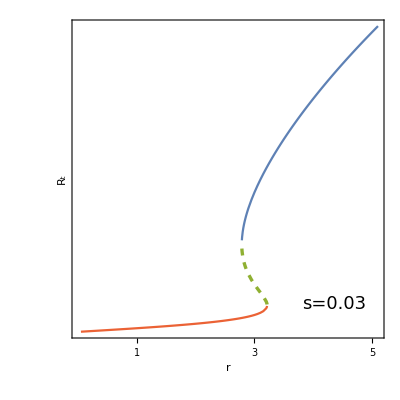

```mathematica
PlotREcoRVbi=Show[ListLinePlot[{RDown,RUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[RMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["R_t",optsLabel1]},FrameTicks->{
{None,None},

{{{5,StyleForm["5",optsScale1],{0.03,0}},{4,StyleForm["4",optsScale1],{0.03,0}},{3,StyleForm["3",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}},{1,StyleForm["1",optsScale1],{0.03,0}},{0,StyleForm["0",optsScale1],{0.03,0}}},None}},Epilog->{Text[StyleForm["s=0.03",optsCentrality],{4.35,8},{0,0}]},AspectRatio->1]
```

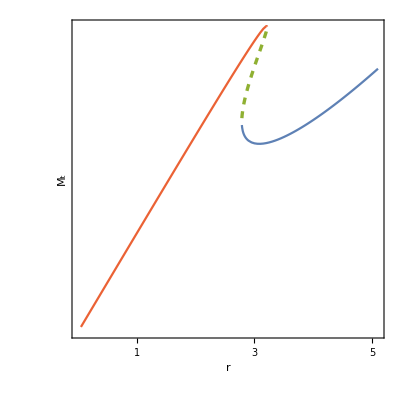

```mathematica
PlotMEcoRVbi=Show[ListLinePlot[{MDown,MUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["M_t",optsLabel1]},FrameTicks->{
{None,None},
{{{5,StyleForm["5",optsScale1],{0.03,0}},{4,StyleForm["4",optsScale1],{0.03,0}},{3,StyleForm["3",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}},{1,StyleForm["1",optsScale1],{0.03,0}},{0,StyleForm["0",optsScale1],{0.03,0}}},None}},AspectRatio->1]
```

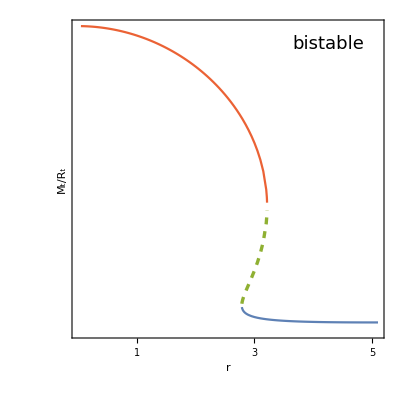

```mathematica
PlotMREcoRVbi=Show[ListLinePlot[{MRRatioDown,MRRatioUp},PlotStyle->{ColorData[97,4],ColorData[97,1]},PlotStyle->Thickness[0.006]],ListLinePlot[MRRatioMiddle, PlotStyle->{ColorData[97,3],Dashed,Thickness[0.006]}],Frame->True,FrameLabel->{StyleForm["r",optsLabel1],StyleForm["M_t/R_t",optsLabel1]},FrameTicks->{
{None,None},

{{{5,StyleForm["5",optsScale1],{0.03,0}},{4,StyleForm["4",optsScale1],{0.03,0}},{3,StyleForm["3",optsScale1],{0.03,0}},{2,StyleForm["2",optsScale1],{0.03,0}},{1,StyleForm["1",optsScale1],{0.03,0}},{0,StyleForm["0",optsScale1],{0.03,0}}},None}},Epilog->{Text[StyleForm["bistable",optsCentrality],{4.25,0.942},{0,0}]},AspectRatio->1]
```

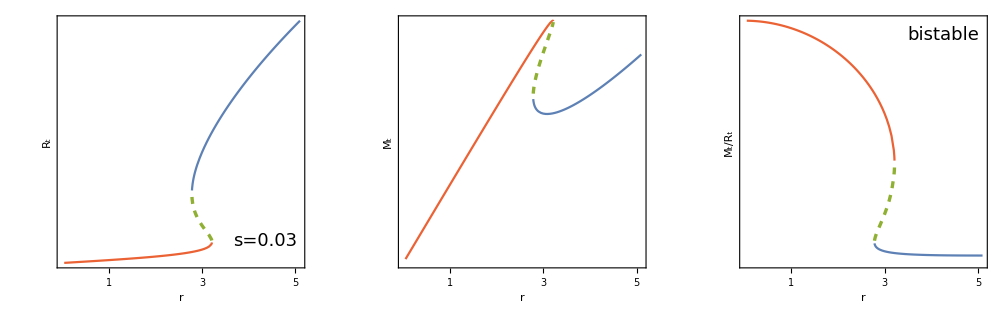

```mathematica
GraphicsRow[{PlotREcoRVbi,PlotMEcoRVbi,PlotMREcoRVbi},ImageSize->1000]
```

This finally reproduces Figure 8 from the manuscript.

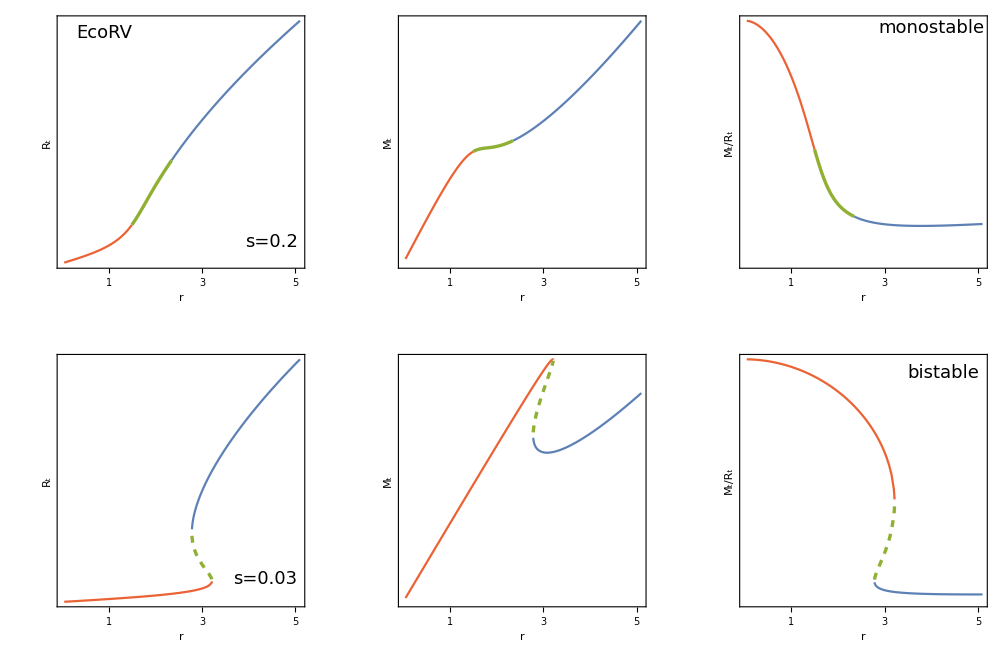

```mathematica
GraphicsGrid[{{PlotREcoRV,PlotMEcoRV,PlotMREcoRV},{PlotREcoRVbi,PlotMEcoRVbi,PlotMREcoRVbi}},ImageSize->1000]
```